```mathematica
silnia[0] = 1;
```

```mathematica
silnia[n_]:=silnia[n - 1] n;
```

```mathematica
0!
```

1

```mathematica
10!
```

3628800

```mathematica
Factorial[10]
```

3628800

```mathematica
silnia[10]
```

3628800

```mathematica
silnia[2]
```

2

```mathematica
2!
```

2

```mathematica
4!
```

24

```mathematica
x = 1;
```

```mathematica
y = x;
```

```mathematica
z:=x;
```

```mathematica
Print[x]
```

1

```mathematica
Print[y]
```

1

```mathematica
Print[z]
```

1

```mathematica
x = 2;
```

```mathematica
Print[x]
```

2

```mathematica
Print[y]
```

1

```mathematica
Print[z]
```

2

```mathematica
Clear[x , y , z]
```

```mathematica
Hold[FullForm[x = 1]]
```

Hold[Set[x,1]]

```mathematica
Hold[FullForm[y = x]]
```

Hold[Set[y,x]]

```mathematica
Hold[FullForm[z:=x]]
```

Hold[SetDelayed[z,x]]

```mathematica
(*podniesienie do potęgi: CTRL + 6*)
```

```mathematica
2^n
```

2^n

```mathematica
Hold[FullForm[2^n]]
```

Hold[Power[2,n]]

```mathematica
Power[2 , n]
```

2^n

```mathematica
(*greckie symbole: ESC pi ESC*)
```

```mathematica
π
```

π

```mathematica
(**)
```

```mathematica
FullSimplify[1 + 2 x + x^2]
```

(1+x)^2

```mathematica
Simplify[1 + 2 x + Power[x , 2]]
```

(1+x)^2

```mathematica
(*strzałka : - >*)
```

```mathematica
FullSimplify[1 + x > 0 , Assumptions->x > 0]
```

True

```mathematica
Hold[FullForm[FullSimplify[1 + x > 0 , Assumptions->x > 0]]]
```

Hold[FullSimplify[Greater[Plus[1,x],0],Rule[Assumptions,Greater[x,0]]]]

```mathematica
FullSimplify[1 + x > 0 ,x > 0]
```

True

```mathematica
True&&True
```

True

```mathematica
True&&False
```

False

```mathematica
True||False
```

True

```mathematica
Hold[FullForm[True&&False]]
```

Hold[And[True,False]]

```mathematica
x = 1;
```

```mathematica
Hold[FullForm[x=1;]]
```

Hold[CompoundExpression[Set[x,1],Null]]

```mathematica
Null
```

```mathematica
Hold[FullForm[xx = 123;yy = 321;Print[xx+yy]]]
```

Hold[CompoundExpression[Set[xx,123],Set[yy,321],Print[Plus[xx,yy]]]]

```mathematica
xx = 123;yy = 321;Print[xx+yy]
```

444

```mathematica
Hold[FullForm[xx = 123;yy = 321;xx+yy]]
```

Hold[CompoundExpression[Set[xx,123],Set[yy,321],Plus[xx,yy]]]

```mathematica
xx = 123;yy = 321;xx+yy
```

444

```mathematica
Hold[FullForm[xx = 123;yy = 321;xx+yy;]]
```

Hold[CompoundExpression[Set[xx,123],Set[yy,321],Plus[xx,yy],Null]]

```mathematica
xx = 123;yy = 321;xx+yy;
```

```mathematica
covidData = Import["https://github.com/CSSEGISandData/COVID-19/raw/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
```

```mathematica
(*covidData*)
```

```mathematica
(*"https://kacpertopol.github.io"*)
```

```mathematica
simpleData = {
{123 , 321 , 123},
{9812938 , 98091823},
{8437 , 1882 , 291},
{123, 333 , 111}
};
```

```mathematica
FullForm[simpleData]
```

List[List[123,321,123],List[9812938,98091823],List[8437,1882,291],List[123,333,111]]

```mathematica
Length[simpleData]
```

4

```mathematica
Dimensions[simpleData]
```

{4}

```mathematica
myList = mojalista[
mojalista[1 , 2] , 
mojalista[3 , 4] , 
mojalista[5 , 6] , 
mojalista[7 , 8]
];
```

```mathematica
Dimensions[
myList]
```

{4,2}

```mathematica
(* [ [ ] ]*)
```

```mathematica
{1 , 2 , 3}[[2]]
```

2

```mathematica
Hold[FullForm[{1 , 2 , 3}[[2]]]]
```

Hold[Part[List[1,2,3],2]]

```mathematica
{1 , 2 , 3}[[-1]]
```

3

```mathematica
{1 , 2 , 3 , 4 ,5 , 6}[[2;;5]]
```

{2,3,4,5}

```mathematica
{1 , 2 , 3 , 4 ,5 , 6}[[2;;]]
```

{2,3,4,5,6}

```mathematica
{1 , 2 , 3 , 4 ,5 , 6}[[;;5]]
```

{1,2,3,4,5}

```mathematica
{1 , 2 , 3 , 4 ,5 , 6}[[-3;;]]
```

{4,5,6}

```mathematica
Length[covidData]
```

290

```mathematica
Dimensions[covidData]
```

{290,999}

```mathematica
covidDataData = covidData[[2;;,5;;]];
```

```mathematica
Dimensions[covidDataData]
```

{289,995}

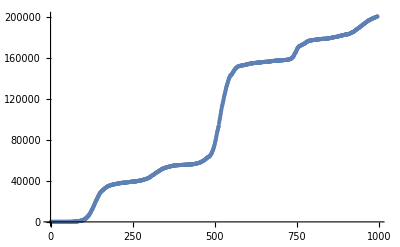

```mathematica
ListPlot[covidDataData[[1]]]
```

```mathematica
Cases[covidData , {_,"Poland" , __}][[1,5;;]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,5,5,11,16,22,31,49,68,103,119,177,238,251,355,425,536,634,749,901,1051,1221,1389,1638,1862,2055,2311,2554,2946,3383,3627,4102,4413,4848,5205,5575,5955,6356,6674,6934,7202,7582,7918,8379,8742,9287,9593,9856,10169,10511,10892,11273,11617,11902,12218,12640,12877,13105,13375,13693,14006,14431,14740,15047,15366,15651,15996,16326,16921,17204,17615,18016,18257,18529,18885,19268,19739,20143,20619,20931,21326,21631,22074,22473,22825,23155,23571,23786,24165,24395,24687,25048,25410,25986,26561,27160,27560,27842,28201,28577,29017,29392,29788,30195,30701,31015,31316,31620,31931,32227,32527,32821,33119,33395,33714,33907,34154,34393,34775,35146,35405,35719,35950,36155,36412,36689,36951,37216,37521,37891,38190,38457,38721,39054,39407,39746,40104,40383,40782,41162,41580,42038,42622,43065,43402,43904,44416,45031,45688,46346,46894,47469,48149,48789,49515,50324,51167,51791,52410,52961,53676,54487,55319,56090,56684,57279,57876,58611,59378,60281,61181,61762,62310,63073,63802,64689,65480,66239,66870,67372,67922,68517,69129,69820,70387,70824,71126,71526,71947,72453,73047,73650,74152,74529,75134,75734,76571,77328,78330,79240,79988,80699,81673,82809,84396,85980,87330,88636,89962,91514,93481,95773,98140,100074,102080,104316,107319,111599,116338,121638,125816,130210,135278,141804,149903,157608,167230,175766,183248,192539,202579,214686,228318,241946,253688,263929,280229,299049,319205,340834,362731,379902,395480,414844,439536,466679,493765,521640,546425,568138,593592,618813,641496,665547,691118,712972,733788,752940,772823,796798,819262,843475,861331,876333,909066,924422,941112,958416,973593,985075,990811,999924,1013747,1028610,1041846,1054273,1063449,1067870,1076180,1088346,1102096,1115201,1126700,1135676,1140572,1147446,1159901,1171854,1182864,1194110,1202700,1207333,1214525,1226883,1239998,1249079,1253957,1257799,1261010,1268634,1281414,1294878,1305774,1312780,1318562,1322947,1330543,1344763,1356882,1365645,1376389,1385522,1390385,1395779,1404905,1414362,1422320,1429612,1435582,1438914,1443804,1450747,1457755,1464448,1470879,1475445,1478119,1482722,1489512,1496665,1502810,1508674,1513385,1515889,1520215,1527016,1533511,1539564,1545530,1550255,1552686,1556685,1563645,1570658,1577036,1583621,1588955,1591497,1596673,1605372,1614446,1623218,1631727,1638767,1642658,1648962,1661109,1673252,1684788,1696885,1706986,1711772,1719708,1735406,1750659,1766490,1781345,1794914,1801083,1811036,1828313,1849424,1868297,1889360,1906632,1917527,1931921,1956974,1984248,2010244,2036700,2058550,2073129,2089869,2120671,2154821,2189966,2221725,2250991,2267964,2288826,2321717,2356970,2387511,2415584,2438542,2448463,2456709,2471617,2499507,2528006,2552898,2574631,2586647,2599850,2621116,2642242,2660088,2675874,2688025,2695327,2704571,2718493,2731256,2742122,2751632,2758856,2762323,2768034,2776927,2785353,2792142,2798617,2803233,2805756,2808052,2811951,2818378,2824425,2829196,2833052,2835083,2838180,2842339,2845762,2849014,2851911,2854079,2855190,2856924,2859261,2861351,2863031,2864546,2865622,2866181,2867187,2868450,2869652,2870595,2871371,2871950,2872283,2872868,2873527,2874092,2874411,2874824,2875136,2875328,2875729,2876289,2876667,2877007,2877243,2877469,2877608,2877819,2878061,2878276,2878466,2878634,2878767,2878840,2879030,2879192,2879336,2879470,2879569,2879638,2879689,2879811,2879912,2880010,2880107,2880215,2880270,2880308,2880403,2880503,2880596,2880670,2880755,2880821,2880865,2880959,2881046,2881151,2881241,2881355,2881424,2881491,2881594,2881718,2881840,2881948,2882066,2882146,2882220,2882327,2882465,2882630,2882786,2882939,2883029,2883120,2883284,2883448,2883624,2883796,2883976,2884098,2884162,2884361,2884557,2884780,2884974,2885185,2885333,2885461,2885676,2885883,2886079,2886291,2886513,2886698,2886805,2887037,2887270,2887485,2887739,2888028,2888231,2888385,2888670,2889036,2889412,2889773,2890161,2890484,2890666,2891071,2891602,2892113,2892642,2893173,2893649,2893919,2894455,2895223,2895947,2896599,2897395,2897935,2898299,2899008,2899888,2900862,2901674,2902591,2903234,2903655,2904631,2905866,2907071,2908432,2909776,2910866,2911549,2912876,2914962,2916969,2918863,2920874,2922401,2923304,2925425,2928065,2931064,2933834,2937069,2939590,2941126,2945056,2950616,2956207,2961923,2968200,2972927,2975880,2982143,2990509,2998891,3008294,3018100,3025247,3030151,3034668,3045102,3060613,3076518,3091713,3104220,3111534,3125179,3143725,3162804,3175769,3190067,3204515,3214023,3230634,3254875,3279787,3303046,3326464,3345388,3357763,3377698,3406129,3434272,3461066,3487254,3507828,3520961,3540061,3569137,3596491,3623452,3649027,3671421,3684671,3704040,3732589,3760048,3785036,3808798,3828248,3839625,3857085,3881349,3903445,3923472,3942864,3958840,3968450,3982257,4000270,4017420,4032796,4043585,4049838,4054865,4064715,4080282,4094608,4108215,4120248,4127428,4133851,4145518,4162715,4179292,4191193,4202090,4213197,4220984,4232386,4248559,4265433,4281482,4298375,4313036,4323482,4343130,4373718,4406553,4443217,4484095,4518218,4547315,4584360,4637776,4695435,4752700,4804390,4852677,4886154,4925270,4981321,5035796,5083332,5129080,5163780,5188184,5223507,5270363,5312450,5348224,5379551,5401615,5415088,5437343,5466198,5495432,5519411,5540302,5553989,5563446,5582217,5602680,5620946,5637646,5651596,5660493,5667054,5680034,5694767,5708827,5721316,5734041,5741739,5747322,5760498,5774938,5788363,5799996,5811109,5818687,5823982,5836672,5851147,5863414,5875072,5885446,5891140,5895304,5905463,5915888,5924876,5933107,5939735,5943227,5945594,5952200,5957940,5962931,5966970,5969071,5969621,5970114,5971998,5973557,5975040,5976364,5977773,5978215,5978596,5980220,5981486,5982664,5983864,5984940,5985251,5985517,5985818,5987341,5988518,5989614,5990853,5991197,5991464,5992820,5993861,5994818,5995674,5996514,5996748,5996935,5997825,5997998,5998909,5999517,6000217,6000416,6000600,6001327,6001893,6002394,6002863,6003297,6003436,6003531,6004041,6004427,6004786,6005101,6005436,6005531,6005596,6006015,6006298,6006547,6006809,6007073,6007156,6007238,6007584,6007840,6008059,6008295,6008550,6008612,6008665,6009003,6009205,6009479,6009726,6009989,6010045,6010090,6010411,6010643,6010871,6010919,6011174,6011239,6011286,6011660,6011984,6012289,6012635,6012979,6013076,6013164,6013859,6014404,6014992,6015634,6016249,6016407,6016526,6017601,6018565,6019633,6020679,6021943,6022227,6022454,6024488,6026134,6027974,6029947,6032078,6032475,6032794,6036042,6038893,6041891,6044923,6048411,6049052,6049640,6054743,6058462,6061946,6065332,6069016,6069665,6070282,6075927,6080398,6084876,6089166,6093571,6094269,6094868,6100827,6105306,6109621,6113843,6118482,6119257,6120028,6120834,6128006,6133274,6138093,6142917,6143682,6144404,6150576,6154969,6158817,6162667,6166596,6167203,6167759,6173059,6176885,6180224,6183676,6186948,6187450,6187928,6193765,6198213,6202436,6206985,6211955,6212603,6213262,6221132,6227259,6233117,6238544,6243975,6244650,6245370,6253044,6258678,6263616,6268049,6272576,6273317,6274048,6280530,6285403,6289672,6293558,6297123,6297431,6297656,6302275,6305467,6308347,6310973,6314705,6315166,6315552,6318840,6321200}

```mathematica
Cases[covidData , {_,"Poland" , __}][[1]][[5;;]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,5,5,11,16,22,31,49,68,103,119,177,238,251,355,425,536,634,749,901,1051,1221,1389,1638,1862,2055,2311,2554,2946,3383,3627,4102,4413,4848,5205,5575,5955,6356,6674,6934,7202,7582,7918,8379,8742,9287,9593,9856,10169,10511,10892,11273,11617,11902,12218,12640,12877,13105,13375,13693,14006,14431,14740,15047,15366,15651,15996,16326,16921,17204,17615,18016,18257,18529,18885,19268,19739,20143,20619,20931,21326,21631,22074,22473,22825,23155,23571,23786,24165,24395,24687,25048,25410,25986,26561,27160,27560,27842,28201,28577,29017,29392,29788,30195,30701,31015,31316,31620,31931,32227,32527,32821,33119,33395,33714,33907,34154,34393,34775,35146,35405,35719,35950,36155,36412,36689,36951,37216,37521,37891,38190,38457,38721,39054,39407,39746,40104,40383,40782,41162,41580,42038,42622,43065,43402,43904,44416,45031,45688,46346,46894,47469,48149,48789,49515,50324,51167,51791,52410,52961,53676,54487,55319,56090,56684,57279,57876,58611,59378,60281,61181,61762,62310,63073,63802,64689,65480,66239,66870,67372,67922,68517,69129,69820,70387,70824,71126,71526,71947,72453,73047,73650,74152,74529,75134,75734,76571,77328,78330,79240,79988,80699,81673,82809,84396,85980,87330,88636,89962,91514,93481,95773,98140,100074,102080,104316,107319,111599,116338,121638,125816,130210,135278,141804,149903,157608,167230,175766,183248,192539,202579,214686,228318,241946,253688,263929,280229,299049,319205,340834,362731,379902,395480,414844,439536,466679,493765,521640,546425,568138,593592,618813,641496,665547,691118,712972,733788,752940,772823,796798,819262,843475,861331,876333,909066,924422,941112,958416,973593,985075,990811,999924,1013747,1028610,1041846,1054273,1063449,1067870,1076180,1088346,1102096,1115201,1126700,1135676,1140572,1147446,1159901,1171854,1182864,1194110,1202700,1207333,1214525,1226883,1239998,1249079,1253957,1257799,1261010,1268634,1281414,1294878,1305774,1312780,1318562,1322947,1330543,1344763,1356882,1365645,1376389,1385522,1390385,1395779,1404905,1414362,1422320,1429612,1435582,1438914,1443804,1450747,1457755,1464448,1470879,1475445,1478119,1482722,1489512,1496665,1502810,1508674,1513385,1515889,1520215,1527016,1533511,1539564,1545530,1550255,1552686,1556685,1563645,1570658,1577036,1583621,1588955,1591497,1596673,1605372,1614446,1623218,1631727,1638767,1642658,1648962,1661109,1673252,1684788,1696885,1706986,1711772,1719708,1735406,1750659,1766490,1781345,1794914,1801083,1811036,1828313,1849424,1868297,1889360,1906632,1917527,1931921,1956974,1984248,2010244,2036700,2058550,2073129,2089869,2120671,2154821,2189966,2221725,2250991,2267964,2288826,2321717,2356970,2387511,2415584,2438542,2448463,2456709,2471617,2499507,2528006,2552898,2574631,2586647,2599850,2621116,2642242,2660088,2675874,2688025,2695327,2704571,2718493,2731256,2742122,2751632,2758856,2762323,2768034,2776927,2785353,2792142,2798617,2803233,2805756,2808052,2811951,2818378,2824425,2829196,2833052,2835083,2838180,2842339,2845762,2849014,2851911,2854079,2855190,2856924,2859261,2861351,2863031,2864546,2865622,2866181,2867187,2868450,2869652,2870595,2871371,2871950,2872283,2872868,2873527,2874092,2874411,2874824,2875136,2875328,2875729,2876289,2876667,2877007,2877243,2877469,2877608,2877819,2878061,2878276,2878466,2878634,2878767,2878840,2879030,2879192,2879336,2879470,2879569,2879638,2879689,2879811,2879912,2880010,2880107,2880215,2880270,2880308,2880403,2880503,2880596,2880670,2880755,2880821,2880865,2880959,2881046,2881151,2881241,2881355,2881424,2881491,2881594,2881718,2881840,2881948,2882066,2882146,2882220,2882327,2882465,2882630,2882786,2882939,2883029,2883120,2883284,2883448,2883624,2883796,2883976,2884098,2884162,2884361,2884557,2884780,2884974,2885185,2885333,2885461,2885676,2885883,2886079,2886291,2886513,2886698,2886805,2887037,2887270,2887485,2887739,2888028,2888231,2888385,2888670,2889036,2889412,2889773,2890161,2890484,2890666,2891071,2891602,2892113,2892642,2893173,2893649,2893919,2894455,2895223,2895947,2896599,2897395,2897935,2898299,2899008,2899888,2900862,2901674,2902591,2903234,2903655,2904631,2905866,2907071,2908432,2909776,2910866,2911549,2912876,2914962,2916969,2918863,2920874,2922401,2923304,2925425,2928065,2931064,2933834,2937069,2939590,2941126,2945056,2950616,2956207,2961923,2968200,2972927,2975880,2982143,2990509,2998891,3008294,3018100,3025247,3030151,3034668,3045102,3060613,3076518,3091713,3104220,3111534,3125179,3143725,3162804,3175769,3190067,3204515,3214023,3230634,3254875,3279787,3303046,3326464,3345388,3357763,3377698,3406129,3434272,3461066,3487254,3507828,3520961,3540061,3569137,3596491,3623452,3649027,3671421,3684671,3704040,3732589,3760048,3785036,3808798,3828248,3839625,3857085,3881349,3903445,3923472,3942864,3958840,3968450,3982257,4000270,4017420,4032796,4043585,4049838,4054865,4064715,4080282,4094608,4108215,4120248,4127428,4133851,4145518,4162715,4179292,4191193,4202090,4213197,4220984,4232386,4248559,4265433,4281482,4298375,4313036,4323482,4343130,4373718,4406553,4443217,4484095,4518218,4547315,4584360,4637776,4695435,4752700,4804390,4852677,4886154,4925270,4981321,5035796,5083332,5129080,5163780,5188184,5223507,5270363,5312450,5348224,5379551,5401615,5415088,5437343,5466198,5495432,5519411,5540302,5553989,5563446,5582217,5602680,5620946,5637646,5651596,5660493,5667054,5680034,5694767,5708827,5721316,5734041,5741739,5747322,5760498,5774938,5788363,5799996,5811109,5818687,5823982,5836672,5851147,5863414,5875072,5885446,5891140,5895304,5905463,5915888,5924876,5933107,5939735,5943227,5945594,5952200,5957940,5962931,5966970,5969071,5969621,5970114,5971998,5973557,5975040,5976364,5977773,5978215,5978596,5980220,5981486,5982664,5983864,5984940,5985251,5985517,5985818,5987341,5988518,5989614,5990853,5991197,5991464,5992820,5993861,5994818,5995674,5996514,5996748,5996935,5997825,5997998,5998909,5999517,6000217,6000416,6000600,6001327,6001893,6002394,6002863,6003297,6003436,6003531,6004041,6004427,6004786,6005101,6005436,6005531,6005596,6006015,6006298,6006547,6006809,6007073,6007156,6007238,6007584,6007840,6008059,6008295,6008550,6008612,6008665,6009003,6009205,6009479,6009726,6009989,6010045,6010090,6010411,6010643,6010871,6010919,6011174,6011239,6011286,6011660,6011984,6012289,6012635,6012979,6013076,6013164,6013859,6014404,6014992,6015634,6016249,6016407,6016526,6017601,6018565,6019633,6020679,6021943,6022227,6022454,6024488,6026134,6027974,6029947,6032078,6032475,6032794,6036042,6038893,6041891,6044923,6048411,6049052,6049640,6054743,6058462,6061946,6065332,6069016,6069665,6070282,6075927,6080398,6084876,6089166,6093571,6094269,6094868,6100827,6105306,6109621,6113843,6118482,6119257,6120028,6120834,6128006,6133274,6138093,6142917,6143682,6144404,6150576,6154969,6158817,6162667,6166596,6167203,6167759,6173059,6176885,6180224,6183676,6186948,6187450,6187928,6193765,6198213,6202436,6206985,6211955,6212603,6213262,6221132,6227259,6233117,6238544,6243975,6244650,6245370,6253044,6258678,6263616,6268049,6272576,6273317,6274048,6280530,6285403,6289672,6293558,6297123,6297431,6297656,6302275,6305467,6308347,6310973,6314705,6315166,6315552,6318840,6321200}

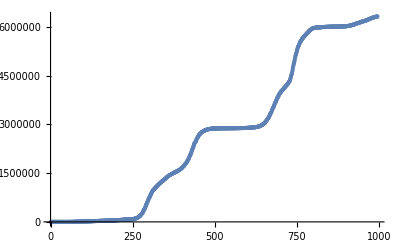

```mathematica
ListPlot[(Cases[covidData , {_,"Poland" , __}][[1]])[[5;;]]]
```

```mathematica
f[x_ , y_]:=If[x^2+y^2<0.75^2,1 , 0];
```

```mathematica
f[2 , 1]
```

0

```mathematica
f[0.5 , 0.5]
```

1

```mathematica
(*&& , ||*)
```

```mathematica
l==p
```

l==p

```mathematica
If[l == p , 1 , 2 , 3]
```

3

```mathematica
l===p
```

False

```mathematica
If[l===p , 1 , 2 , 3]
```

2

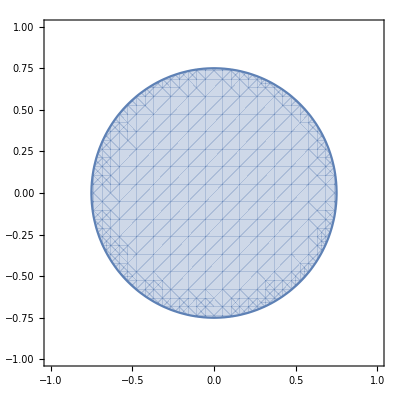

```mathematica
RegionPlot[f[x , y]===1 ,{x , -1 , 1},{y , -1 , 1}]
```

```mathematica
x
```

x

```mathematica
Clear[x , y , z]
```

```mathematica
Integrate[f[x , y] , {x , -1 , 1} , {y , -1 , 1}]
```

1.76715

```mathematica
N[π (3/4)^2]
```

1.76715